```mathematica
data = Import["/Users/eduardopeinado/Library/CloudStorage/Dropbox/InverseHiggsStabilityDM/SIcrosssectionlimits/HEPData.csv"];
```

```mathematica
data={{9.,1.0199214818092348*^-46},{11.,2.7574936853333923*^-47},{13.,1.2291221601112764*^-47},{16.,6.00362024779195*^-48},{17.,5.3348205653471906*^-48},{19.,3.896848454379515*^-48},{21.,3.323727092028127*^-48},{23.,2.968490798015544*^-48},{26.,2.6155789945448642*^-48},{29.,2.368424326343989*^-48},{32.,2.287306921114239*^-48},{36.,2.104230188726472*^-48},{40.,2.115332912193402*^-48},{43.,2.2352757396556997*^-48},{46.,2.1976972131899662*^-48},{65.,2.505718637217682*^-48},{91.,3.195915359877079*^-48},{129.,3.8815261565995756*^-48},{182.,5.594168215658859*^-48},{256.,7.656920668880268*^-48},{361.,1.0628391162129717*^-47},{508.,1.4393418129001175*^-47},{1008.,2.9420174519256495*^-47},{2000.,5.819333597956092*^-47},{5000.,1.422698125240569*^-46},{10000.,2.884421626978188*^-46}}
```

{{9.,1.01992×10^-46},{11.,2.75749×10^-47},{13.,1.22912×10^-47},{16.,6.00362×10^-48},{17.,5.33482×10^-48},{19.,3.89685×10^-48},{21.,3.32373×10^-48},{23.,2.96849×10^-48},{26.,2.61558×10^-48},{29.,2.36842×10^-48},{32.,2.28731×10^-48},{36.,2.10423×10^-48},{40.,2.11533×10^-48},{43.,2.23528×10^-48},{46.,2.1977×10^-48},{65.,2.50572×10^-48},{91.,3.19592×10^-48},{129.,3.88153×10^-48},{182.,5.59417×10^-48},{256.,7.65692×10^-48},{361.,1.06284×10^-47},{508.,1.43934×10^-47},{1008.,2.94202×10^-47},{2000.,5.81933×10^-47},{5000.,1.4227×10^-46},{10000.,2.88442×10^-46}}

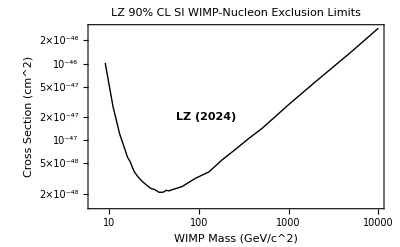

```mathematica
P1=ListLogLogPlot[data,Joined->True,PlotStyle->{Black,Thick},Frame->True,FrameLabel->{"WIMP Mass (GeV/c^2)","Cross Section (cm^2)"},PlotLabel->"LZ 90% CL SI WIMP-Nucleon Exclusion Limits",Epilog->{Text[Style["LZ (2024)",Black,Bold],Scaled[{0.4,0.5}]],Red,Thick,Line[{{10,2.12*10^-48},{10000,2.12*10^-48}}]}]
```

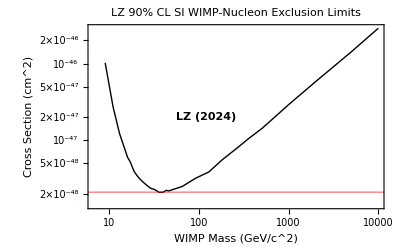

```mathematica
P1 = ListLogLogPlot[
  data,
  Joined -> True,
  PlotStyle -> {Black, Thick},
  Frame -> True,
  FrameLabel -> {"WIMP Mass (GeV/c^2)", "Cross Section (cm^2)"},
  PlotLabel -> "LZ 90% CL SI WIMP-Nucleon Exclusion Limits",
  GridLines -> {None, {2.12*10^-48}},
  GridLinesStyle -> Directive[Red, Thick],
  Epilog -> {
    Text[Style["LZ (2024)", Black, Bold], Scaled[{0.4, 0.5}]]
  }
]
```

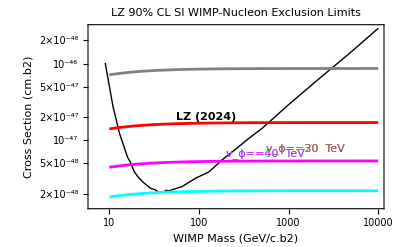

```mathematica
P1=ListLogLogPlot[data,Joined->True,PlotStyle->{Black,Thick},Frame->True,FrameLabel->{"WIMP Mass (GeV/c.b2)","Cross Section (cm.b2)"},PlotLabel->"LZ 90% CL SI WIMP-Nucleon Exclusion Limits",Epilog->{Text[Style["LZ (2024)",Black,Bold],Scaled[{0.4,0.5}],{-4,9}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Cyan],Scaled[{0.6,0.3}],{-9,12}],Text[Style[TraditionalForm[Subscript[v,ϕ]==40 " TeV"],Magenta],Scaled[{0.6,0.3}],{-9,0}],Text[Style[TraditionalForm[Subscript[v,ϕ]==30 " TeV"],Red],Scaled[{0.6,0.3}],{-9,-12.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==20 " TeV"],Gray],Scaled[{0.6,0.3}],{-9,-33}]}];Show[P1,P2]
```

```mathematica
Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Cyan],Scaled[{0.6,0.3}],{-1,5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Magenta],Scaled[{0.6,0.3}],{-3,-2}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Red],Scaled[{0.6,0.3}],{-3,-9.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Red],Scaled[{0.6,0.3}],{-3,-21}]
```

```mathematica
GeV=5.06 10^13 1/cm
```

(5.06×10^13)/cm

```mathematica
cm=1
```

1

```mathematica
A1=(mDM/(mDM+1))^2g^4/(Pi 9 (g 50 10^3)^4)1/GeV^2/.cm->1;A2=(mDM/(mDM+1))^2 g^4/(Pi 9 (g 40 10^3)^4)1/GeV^2;A3=(mDM/(mDM+1))^2 g^4/(Pi 9 (g 30 10^3)^4)1/GeV^2;A4=(mDM/(mDM+1))^2 g^4/(Pi 9 (g 20 10^3)^4)1/GeV^2;
```

```mathematica
A1/.mDM->10.
```

1.82659×10^-48

```mathematica
A2/.mDM->10
```

4.45945×10^-48

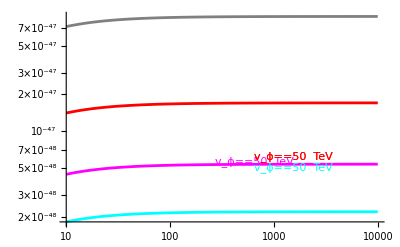

```mathematica
P2=LogLogPlot[{A1,A2,A3,A4},{mDM,10,10^4},PlotStyle->{Cyan,Magenta,Red,Gray},Epilog->{Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Cyan],Scaled[{0.6,0.3}],{-1,7}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Magenta],Scaled[{0.6,0.3}],{-3,-4}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Red],Scaled[{0.6,0.3}],{-3,-9.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Red],Scaled[{0.6,0.3}],{-3,-21}]}]
```

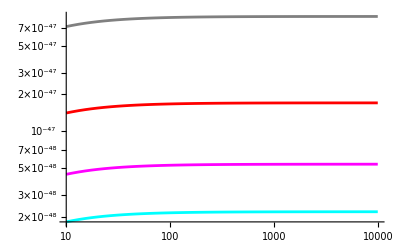

```mathematica
P2=LogLogPlot[{A1,A2,A3,A4},{mDM,10,10^4},PlotStyle->{Cyan,Magenta,Red,Gray}]
```

```mathematica
Text[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Gray],Scaled[{0.6,0.3}],{-3,-21}
```

```mathematica
A4
```

(8.63349×10^-47 mDM^2)/(1+mDM)^2

```mathematica
P2
```

-Graphics-

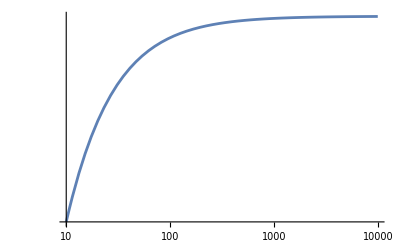

```mathematica
P3=LogLogPlot[A4,{mDM,10,10^4}]
```

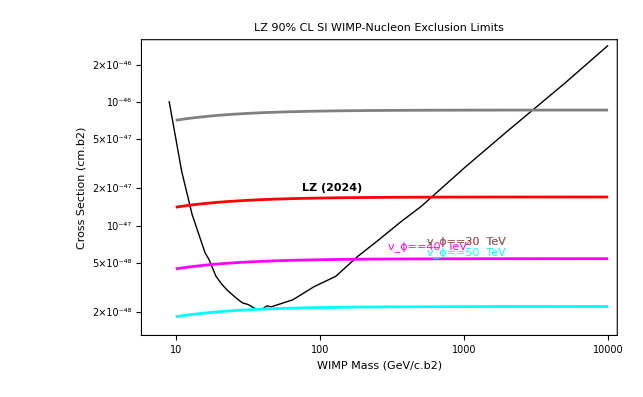

```mathematica
Show[P1,P2]
```

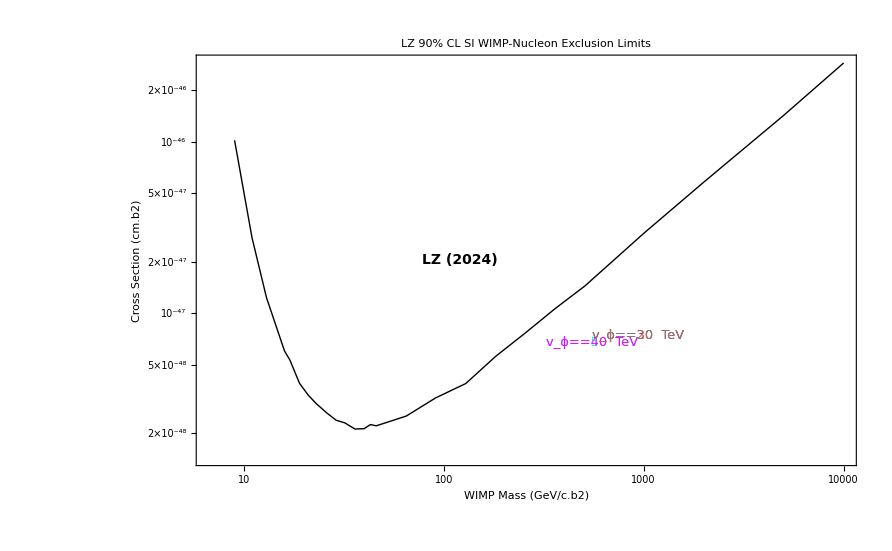

```mathematica
ListLogLogPlot[data,Joined->True,PlotStyle->{Black,Thick},Frame->True,(*Customize axis labels*)FrameLabel->{Style["WIMP Mass (GeV/c.b2)","Times",14,Bold],Style["Cross Section (cm.b2)","Times",14,Bold]},(*Customize plot title*)PlotLabel->Style["LZ 90% CL SI WIMP-Nucleon Exclusion Limits","Helvetica",16,Bold],(*Customize annotations*)Epilog->{Text[Style["LZ (2024)","Arial",Black,Bold,14],Scaled[{0.4,0.5}],{-4,9}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],"Courier",Cyan,13],Scaled[{0.6,0.3}],{-9,12}],Text[Style[TraditionalForm[Subscript[v,ϕ]==40 " TeV"],"Courier",Magenta,13],Scaled[{0.6,0.3}],{-9,0}],Text[Style[TraditionalForm[Subscript[v,ϕ]==30 " TeV"],"Courier",Red,13],Scaled[{0.6,0.3}],{-9,-12.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==20 " TeV"],"Courier",Gray,13],Scaled[{0.6,0.3}],{-9,-33}]}]
```

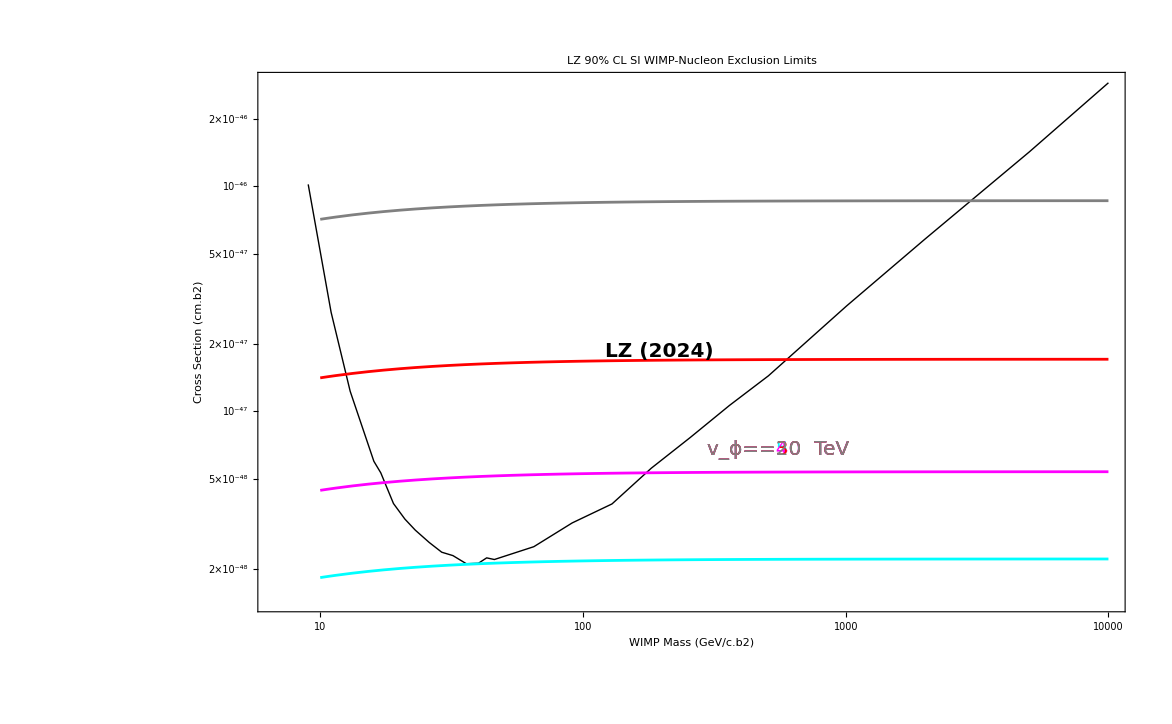

```mathematica
P3=ListLogLogPlot[data,Joined->True,PlotStyle->{Black,Thick},Frame->True,(*Axis labels with font size 20*)FrameLabel->{Style["WIMP Mass (GeV/c.b2)","Times",20,Bold],Style["Cross Section (cm.b2)","Times",20,Bold]},(*Title with font size 20*)PlotLabel->Style["LZ 90% CL SI WIMP-Nucleon Exclusion Limits","Helvetica",20,Bold],(*Epilog annotations with font size 20*)Epilog->{Text[Style["LZ (2024)","Arial",Black,Bold,20],Scaled[{0.4,0.5}],{-1,9}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],"Courier",Cyan,20],Scaled[{0.6,0.3}],{-6,10}],Text[Style[TraditionalForm[Subscript[v,ϕ]==40 " TeV"],"Courier",Magenta,20],Scaled[{0.6,0.3}],{-6,1}],Text[Style[TraditionalForm[Subscript[v,ϕ]==30 " TeV"],"Courier",Red,20],Scaled[{0.6,0.3}],{-6,-10.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==20 " TeV"],"Courier",Gray,20],Scaled[{0.6,0.3}],{-6,-26}]}];Show[P3,P2]
```

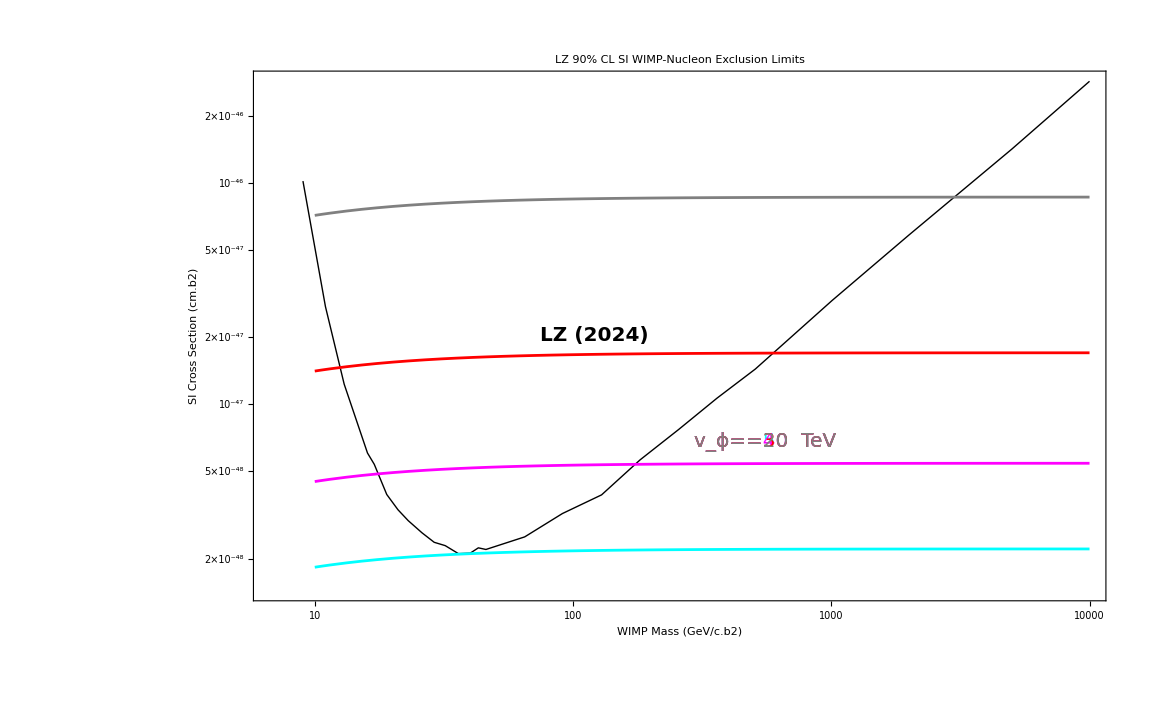

```mathematica
P4=ListLogLogPlot[data,Joined->True,PlotStyle->{Black,Thick},Frame->True,(*Axis labels with font size 20*)FrameLabel->{Style["WIMP Mass (GeV/c.b2)","Times",20,Bold],Style["SI Cross Section (cm.b2)","Times",20,Bold]},(*Axis number size*)FrameTicksStyle->Directive["Times",20],(*Title with font size 20*)PlotLabel->Style["LZ 90% CL SI WIMP-Nucleon Exclusion Limits","Helvetica",20,Bold],(*Epilog annotations with font size 20*)Epilog->{Text[Style["LZ (2024)","Arial",Black,Bold,20],Scaled[{.4,0.5}],{-1,10}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],"Courier",Cyan,20],Scaled[{0.6,0.3}],{-6,9}],Text[Style[TraditionalForm[Subscript[v,ϕ]==40 " TeV"],"Courier",Magenta,20],Scaled[{0.6,0.3}],{-6,1}],Text[Style[TraditionalForm[Subscript[v,ϕ]==30 " TeV"],"Courier",Red,20],Scaled[{0.6,0.3}],{-6,-10.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==20 " TeV"],"Courier",Gray,20],Scaled[{0.6,0.3}],{-6,-25}]}];Show[P4,P2]
```

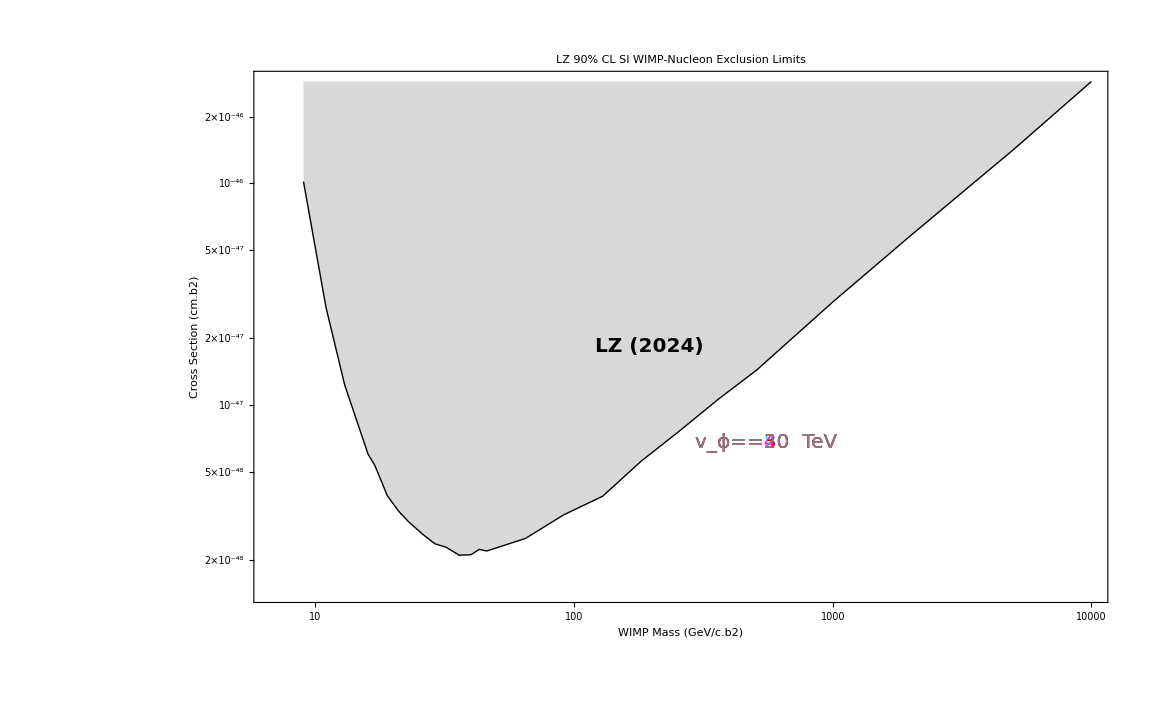

```mathematica
P5=ListLogLogPlot[data,Joined->True,PlotStyle->{Black,Thick},Frame->True,FrameLabel->{Style["WIMP Mass (GeV/c.b2)","Times",20,Bold],Style["Cross Section (cm.b2)","Times",20,Bold]},PlotLabel->Style["LZ 90% CL SI WIMP-Nucleon Exclusion Limits","Helvetica",20,Bold],Filling->Top,FillingStyle->Directive[Gray,Opacity[0.3]],Epilog->{Text[Style["LZ (2024)","Arial",Black,Bold,20],Scaled[{0.4,0.5}],{-1,9}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],"Courier",Cyan,20],Scaled[{0.6,0.3}],{-6,10}],Text[Style[TraditionalForm[Subscript[v,ϕ]==40 " TeV"],"Courier",Magenta,20],Scaled[{0.6,0.3}],{-6,1}],Text[Style[TraditionalForm[Subscript[v,ϕ]==30 " TeV"],"Courier",Red,20],Scaled[{0.6,0.3}],{-6,-10.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==20 " TeV"],"Courier",Gray,20],Scaled[{0.6,0.3}],{-6,-26}]}]
```

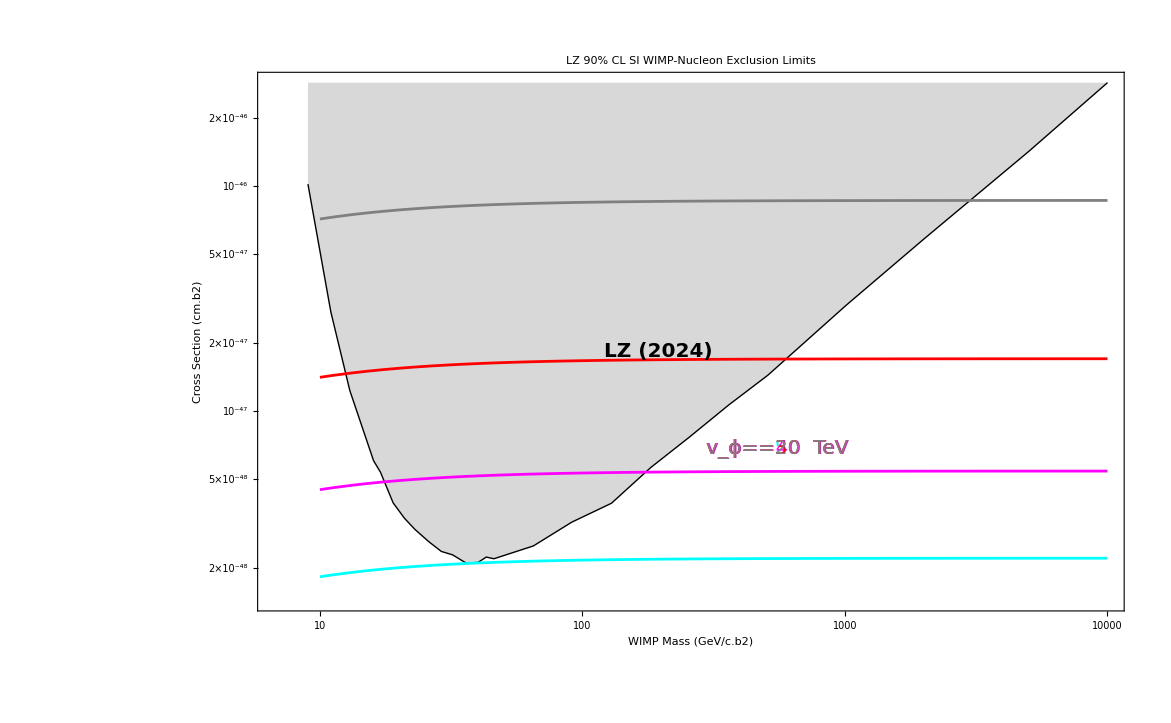

```mathematica
Show[P5,P2]
```

```mathematica
?PlotRange
```